```mathematica
Off[General::"spell",General::"spell1"];
$TextStyle={FontSize->20,FontWeight->"Plain",FontFamily->"Times",FontSlant->"Plain"};
```

## Definição das coordenadas do condutores

### Cabos de fase

Dados do condutor

```mathematica
r0=7.3914*10^-3/2;   (* ⟹ [m] ⟸ *)
r1=29.591*10^-3/2;

Rdcϕ=6.114292531162*10^-5;  (* ⟹ [Ω/m] ⟸⟹ @ 25^o ⟸*)

ρϕ=Rdcϕ*Pi*(r1^2-r0^2);

σϕ=1/ρϕ;
```

Raio do Feixe

```mathematica
raio=1;
```

Número de Subcondutores

```mathematica
nfase=3;
ns=7;
```

Flexa e Desvio da Fase Central

```mathematica
flexacond=23.67;
Δfasecentral=2.0;
```

Distrubuição dos subcondutores no FEIXE

```mathematica
Δx=Table[raio*Sin[(k-1)*2*Pi/ns],{k,1,ns}];
Δy=Table[-raio*Cos[(k-1)*2*Pi/ns],{k,1,ns}];
```

Coordenadas dos centros dos Feixes

```mathematica
cx={-10.5,0,10.5};
cy=flexacond+raio+{12,12+Δfasecentral,12};
```

### Cabos Pára-raios

Dados dos Cabos PR  Aço 3/8"

```mathematica
rpr=4.57*10^-3;

Rdcpr=4.19*10^-3;

ρpr=Rdcpr*Pi*rpr^2;

σpr=1/ρpr;

μpr=80*μo;
```

coordenadas e flexas. Obs: A ordenada do cabo é definida a partir da maior ordenada dos condutores;

```mathematica
npr=2;
xpr=9;
ypr=Max[cy]+9;
flexapr=17.5;
```

### Tabelas das Coordenadas e representação gráfica dos condutores ao meio do Vão

```mathematica
xcond=Table[0,{i,1,nfase*ns}];
contx=1;
For[ksub=1,ksub≤ns,ksub++,For[kfase=1,kfase<=nfase,kfase++,xcond[[contx]]=cx[[kfase]]+Δx[[ksub]];contx=contx+1]];Clear[contx,ksub];

ycond=Table[0,{i,1,nfase*ns}];
conty=1;
For[ksub=1,ksub≤ns,ksub++,For[kfase=1,kfase<=nfase,kfase++,ycond[[conty]]=cy[[kfase]]+Δy[[ksub]];conty=conty+1]];Clear[conty,ksub];
```

```mathematica
x=Table[If[i≤nfase,xcond[[i]],If[i≤nfase+1,-xpr,If[i≤nfase+2,xpr,xcond[[i-2]]]]],{i,1,ns*nfase+2}];
y=Table[If[i≤nfase,ycond[[i]]-2/3*flexacond,If[i≤nfase+2,ypr-2/3*flexapr,ycond[[i-2]]-2/3*flexacond]],{i,1,ns*nfase+2}];
```

```mathematica
xy2=Thread[{x,y}];
```

```mathematica
mostra2={Circle[#,.25]}&/@xy2;
```

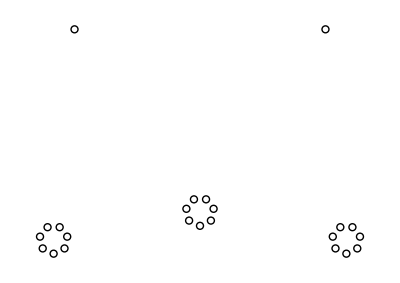

```mathematica
t2=Show[Graphics[mostra2],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->All,FrameLabel->{"(m)","(m)"}]
```

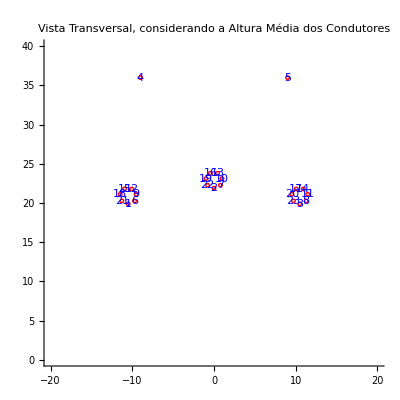

```mathematica
Do[Subscript[aa, k]=Graphics[{RGBColor[1,0,0],Circle[{x[[k]],y[[k]]},0.22]}],{k,1,nfase*ns+2}];
$TextStyle={FontSize->10,FontWeight->"Bold",FontFamily->"Times"};
Do[Subscript[text, k]=Graphics[{RGBColor[0,0,1],Text[k,{x[[k]],y[[k]]}]}],{k,1,nfase*ns+2}];
Show[{Table[Subscript[aa, k],{k,1,nfase*ns+2}],Table[Subscript[text, k],{k,1,nfase*ns+2}]},PlotRange->{{-20,20},{0,40}},Axes->True,AspectRatio->1,PlotLabel->"Vista Transversal, considerando a Altura Média dos Condutores"]
```

### Dados do Meio

Parâmetros do Ar

```mathematica
μo=4.0*Pi*10^-7;
ϵo=1.0/(36*π*10^9);
```

Dados do Solo

```mathematica
σearth=10^-3;                                 (* ⟹ Condutividade do Solo ⟸ *)
```

## Entrada de Dados

Cálculo da Impedância Longitudinal (Na penúltima linha a variável trans determina se a saída será transposta ou não (1 ou 0, respectivamente)

```mathematica
zff[s1_]:=Block[{s,ρ0,ρ1,k,n,d,ziϕ,kpr,ρp,zipr,zi,p,ze,z,z1,z2,zf,zp,zm,ztr,trans},s=s1;
ρ0=r0*Sqrt[μo*σϕ*s];
ρ1=r1*Sqrt[μo*σϕ*s];

k=Sqrt[s*μo/σϕ]/(2*Pi*r1);
n=BesselI[0,ρ1]*BesselK[1,ρ0]+BesselI[1,ρ0]*BesselK[0,ρ1];
d=BesselI[1,ρ1]*BesselK[1,ρ0]-BesselI[1,ρ0]*BesselK[1,ρ1];

ziϕ=k*n/d;

kpr=Sqrt[s*μpr/σpr]/(2*Pi*rpr);
ρp=rpr*Sqrt[μpr*σpr*s];
zipr=kpr*BesselI[0,ρp]/BesselI[1,ρp];

zi=Table[If[i==j,If[i==(nfase+1) ∨ i==(nfase+2),zipr,ziϕ],0],{i,1,ns*nfase+2},{j,1,ns*nfase+2}];

p=1/Sqrt[s*μo*(σearth+s*ϵo)];

ze=s*(μo/(2*Pi))*Log[Table[If[i==j,If[i==(nfase+1)∨i==(nfase+2),2*(y[[i]]+p)/rpr,2*(y[[i]]+p)/r1],(Sqrt[(y[[i]]+y[[j]]+2*p)^2+(x[[i]]-x[[j]])^2]/Sqrt[(y[[i]]-y[[j]])^2+(x[[i]]-x[[j]])^2])],{i,1,ns*nfase+2},{j,1,ns*nfase+2}]];


z=zi+ze;

(*Eliminação do Cabos Condutores*)

z1=Table[0,{i,1,ns*nfase+2},{j,1,ns*nfase+2}];
z2=Table[0,{i,1,ns*nfase+2},{j,1,ns*nfase+2}];

(*Eliminação das Linhas*)

For[i=(ns-1)*nfase+2,i≥0,If[i<=nfase+2,i--,i=i-nfase],For[linha=nfase,linha≥1,linha--,For[j=1,j≤ns*nfase+2,j++,If[i<(nfase+2),z1[[i+1,j]]=z[[i+1,j]],z1[[i+linha,j]]=z[[i+linha,j]]-z[[linha,j]]]]]];Clear[i,j,linha];


(*Eliminação das Colunas*)

For[j=(ns-1)*nfase+2,j≥0,If[j<=nfase+2,j--,j=j-nfase],For[coluna=nfase,coluna≥1,coluna--,For[i=1,i≤ns*nfase+2,i++,If[j<(nfase+2),z2[[i,j+1]]=z1[[i,j+1]],z2[[i,j+coluna]]=z1[[i,j+coluna]]-z1[[i,coluna]]]]]];
Clear[i,j,coluna];


zf=1000*(z2[[Range[1,nfase],Range[1,nfase]]]-z2[[Range[1,nfase],Range[nfase+1,ns*nfase+2]]].Inverse[z2[[Range[nfase+1,ns*nfase+2],Range[nfase+1,ns*nfase+2]]]].z2[[Range[nfase+1,ns*nfase+2],Range[1,nfase]]]);

zp=(1/nfase)*Sum[zf[[i,i]],{i,1,nfase}];

soma=0;
For[linha=1,linha<nfase,linha++,For[coluna=linha+1,coluna≤nfase,coluna++,soma=soma+zf[[linha,coluna]]]];
zm=(1/nfase)*soma;
Clear[linha,coluna,soma];


ztr=Table[If[i==j,zp,zm],{i,1,3},{j,1,3}];
trans=1;
Return[If[trans==0,zf,ztr]]];
```

Cálculo da Admitância Transversal  (Na penúltima linha a variável trans determina se a saída será transposta ou não (1 ou 0,respectivamente)

```mathematica
pp=1/(2*Pi*ϵo)*Log[Table[If[i==j,If[i==nfase+1∨i==nfase+2,2*y[[i]]/rpr,2*y[[i]]/r1],(Sqrt[(y[[i]]+y[[j]])^2+(x[[i]]-x[[j]])^2]/Sqrt[(y[[i]]-y[[j]])^2+(x[[i]]-x[[j]])^2])],{i,1,nfase*ns+2},{j,1,nfase*ns+2}]];

(*=== Admitância Transversal ===*)

pp1=Table[0,{i,1,ns*nfase+2},{j,1,ns*nfase+2}];
pp2=Table[0,{i,1,ns*nfase+2},{j,1,ns*nfase+2}];


For[i=(ns-1)*nfase+2,i≥0,If[i<=nfase+2,i--,i=i-nfase],For[linha=nfase,linha≥1,linha--,For[j=1,j≤ns*nfase+2,j++,If[i<(nfase+2),pp1[[i+1,j]]=pp[[i+1,j]],pp1[[i+linha,j]]=pp[[i+linha,j]]-pp[[linha,j]]]]]];Clear[i,j,linha];

For[j=(ns-1)*nfase+2,j≥0,If[j<=nfase+2,j--,j=j-nfase],For[coluna=nfase,coluna≥1,coluna--,For[i=1,i≤ns*nfase+2,i++,If[j<(nfase+2),pp2[[i,j+1]]=pp1[[i,j+1]],pp2[[i,j+coluna]]=pp1[[i,j+coluna]]-pp1[[i,coluna]]]]]];
Clear[i,j,coluna];

cf=Inverse[(pp2[[Range[1,nfase],Range[1,nfase]]]-pp2[[Range[1,nfase],Range[nfase+1,ns*nfase+2]]].Inverse[pp2[[Range[nfase+1,ns*nfase+2],Range[nfase+1,ns*nfase+2]]]].pp2[[Range[nfase+1,ns*nfase+2],Range[1,nfase]]])];

yff[s1_]:=Block[{s,yf,yp,ym,ytr,trans},s=s1;

yf=1000*s*cf;
yp=(1/nfase)*Sum[yf[[i,i]],{i,1,nfase}];

soma=0;
For[linha=1,linha<nfase,linha++,For[coluna=linha+1,coluna≤nfase,coluna++,soma=soma+yf[[linha,coluna]]]];
ym=(1/nfase)*soma;
Clear[linha,coluna,soma];

ytr=Table[If[i==j,yp,ym],{i,1,3},{j,1,3}];

trans=1;
Return[If[trans==0,yf,ytr]]];
```

Cálculos dos parâmetros da Linha ( Matriz A, Admitância Característica, eYbarra)

```mathematica
matrixA[s1_]:=Block[{s,A,L},s=s1;
L=2722;
A=MatrixExp[(-1)*L*MatrixPower[zff[s].yff[s],0.5]];
Return[A]];

ycar[s1_]:=Block[{s,yc},s=s1;
yc=Inverse[zff[s]].MatrixPower[zff[s].yff[s],0.5];
Return[yc]];

func1[s1_]:=(IdentityMatrix[3]+MatrixPower[matrixA[s1],2]).Inverse[(IdentityMatrix[3]-MatrixPower[matrixA[s1],2])];
func2[s1_]:=(-2)*matrixA[s1].Inverse[(IdentityMatrix[3]-MatrixPower[matrixA[s1],2])];


ydiag[s1_]:=ycar[s1].func1[s1];
yoff[s1_]:=ycar[s1].func2[s1];
```

```mathematica
ypro=ycar[ⅈ*2*π*60][[1,1]]-ycar[ⅈ*2*π*60][[1,2]]
```

0.00582422+0.000120185 ⅈ

```mathematica
pc=(765.000)^2*Re[ypro]
```

3408.48

```mathematica
zc=Inverse[ycar[ⅈ*2*π*60]]
```

{{315.653-24.6299 ⅈ,144.029-21.0883 ⅈ,144.029-21.0883 ⅈ},{144.029-21.0883 ⅈ,315.653-24.6299 ⅈ,144.029-21.0883 ⅈ},{144.029-21.0883 ⅈ,144.029-21.0883 ⅈ,315.653-24.6299 ⅈ}}

```mathematica
(765.000)^2/Re[zc[[1,1]]-zc[[1,2]]]
```

3409.93

```mathematica
zc[[1,1]]-zc[[1,2]]
```

171.624-3.54153 ⅈ

```mathematica
zc[[1,1]]+2*zc[[1,2]]
```

603.712-66.8066 ⅈ

```mathematica
zff[ⅈ*2*π*60]//MatrixForm
```

(0.104038+0.584927 ⅈ | 0.0948812+0.363156 ⅈ | 0.0948812+0.363156 ⅈ
0.0948812+0.363156 ⅈ | 0.104038+0.584927 ⅈ | 0.0948812+0.363156 ⅈ
0.0948812+0.363156 ⅈ | 0.0948812+0.363156 ⅈ | 0.104038+0.584927 ⅈ)

```mathematica
va=(750.000/Sqrt[3]);
vb=va*Exp[-ⅈ*2*Pi/3];
vc=va*Exp[ⅈ*2*Pi/3];
vpr=0;
ten={va,vb,vc,vpr,vpr,va,vb,vc,va,vb,vc,va,vb,vc,va,vb,vc,va,vb,vc,va,vb,vc}
```

{433.013,-216.506-375. ⅈ,-216.506+375. ⅈ,0,0,433.013,-216.506-375. ⅈ,-216.506+375. ⅈ,433.013,-216.506-375. ⅈ,-216.506+375. ⅈ,433.013,-216.506-375. ⅈ,-216.506+375. ⅈ,433.013,-216.506-375. ⅈ,-216.506+375. ⅈ,433.013,-216.506-375. ⅈ,-216.506+375. ⅈ,433.013,-216.506-375. ⅈ,-216.506+375. ⅈ}

```mathematica
ql=Inverse[pp].ten;
qltempo=ql*Exp[ⅈ*2*π*60*t];
```

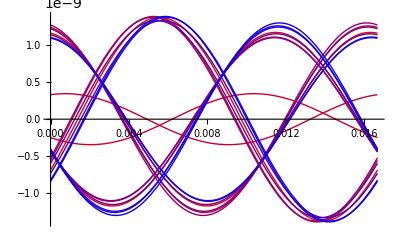

```mathematica
Block[{$DisplayFunction=Identity},
Do[Subscript[plot, n]=Plot[Re[qltempo[[n]]],{t,0,1/60},PlotRange->All,PlotStyle->RGBColor[1-n/23,0,n/23]],{n,1,23}]]
Show[Table[Subscript[plot, cc],{cc,1,23}]]
```

```mathematica
angalfad=Table[0,{i,1,ns*nfase+2},{j,1,ns*nfase+2}];

alfa=angalfad[[i,j]]=Table[If[i==j,0,ArcTan[x[[j]]-(10^(-15)+x[[i]]),(y[[j]]-y[[i]])]],{i,1,ns*nfase+2},{j,1,ns*nfase+2}];
```

Set::pspec: Part specification i is neither an integer nor a list of integers.

```mathematica
alfah=Table[0,{i,1,ns*nfase+2},{j,1,ns*nfase+2}];
alfa2=Table[If[i==j,(-1)*N[Pi/2],(-1)*ArcTan[x[[j]]-(10^(-15)+x[[i]]),(2*y[[j]])]],{i,1,ns*nfase+2},{j,1,ns*nfase+2}];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------*)
(*-------------------------------------------- Campo Elétrico ------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
matrr=Table[If[i==nfase+1∨i==nfase+2,rpr,r1],{i,1,ns*nfase+2}];


kk=Table[Sum[If[i==j,0,(2*((((matrr[[i]])/(Sqrt[(x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2]))^h*Cos[h(γ-alfa2[[i,j]])])-(((matrr[[i]])/(Sqrt[(x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2]))^h*Cos[h(γ-alfa[[i,j]])]))) ],{h,1,2}],{i,1,ns*nfase+2},{j,1,ns*nfase+2}];

jj=	
	Table[Sum[(2*((((matrr[[i]])/(2*y[[i]]))^h*Cos[h(γ-alfa2[[i,i]])]))),{h,1,2}],{i,1,ns*nfase+2}];
```

```mathematica
(*----------------------------------------- Campo Elétrico Superficial ------------------------------------------*)



camp=Table[Sum[If[j==i,0,(((ql[[j]])/(ϵo*matrr[[i]]))*kk[[i,j]])],{j,1,ns*nfase+2}]+((ql[[i]])/(ϵo*matrr[[i]])*(1+jj[[i]])),{i,1,ns*nfase+2}];



campreall=Re[camp];                              (*Fasor*)
campimm=Im[camp];

(* Campo Elétrico no Domínio do Tempo*)

campsupertempo=Table[campreall[[l]]*Cos[ωt]-campimm[[l]]*Sin[ωt],{l,1,ns*nfase+2}];
```

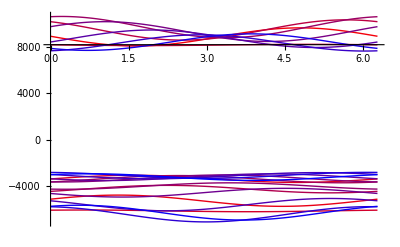

```mathematica
Block[{$DisplayFunction=Identity},
Do[Subscript[plotcamp, n]=Plot[Re[campreall[[n]]],{γ,0,2*π},PlotRange->All,PlotStyle->RGBColor[1-n/23,0,n/23]],{n,1,23}]]
Show[Table[Subscript[plotcamp, cc],{cc,1,23}]]
```